# QED Processes

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
Quit []
```

### Options

## 1. Muon Production - e^- e^+ -> μ^- μ^+

## Tree-Level

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

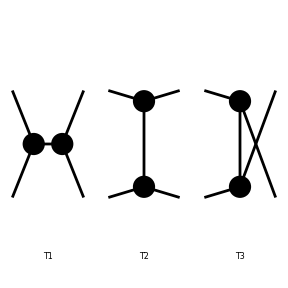

```mathematica
tmp=CreateTopologies[0,2->2, Adjacencies->3];
Paint[tmp];
```

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 1 Generic, 1 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

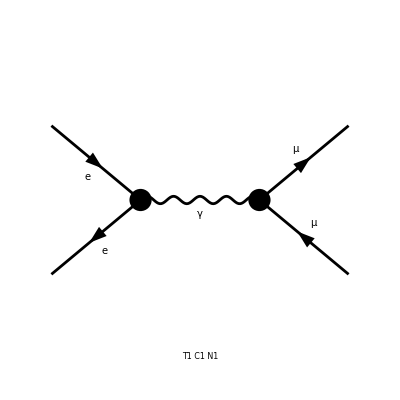

```mathematica
imp=InsertFields[tmp, {F[2,{1}], -F[2,{1}]} -> {F[2,{2}], -F[2,{2}]},QEDOnly];
Paint[imp,PaintLevel->{Classes}];
```

## One-Loop

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 4 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 5 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 6 aebf/cfde/egfhghgh.m, 0 diagrams

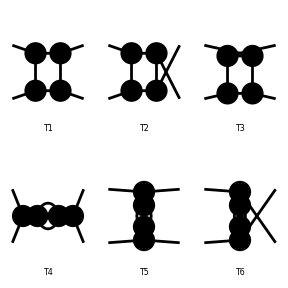

```mathematica
tmp1=CreateTopologies[1,2->2, Adjacencies->3,ExcludeTopologies->{Tadpoles,WFCorrections,Triangles}];
Paint[tmp1];
```

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 3 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 5 Classes insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebe/cfdf/egfhghgh.m, 0 diagrams

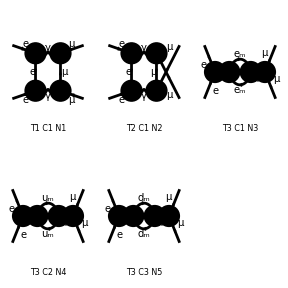

```mathematica
imp1=InsertFields[tmp1,{F[2,{1}], -F[2,{1}]} -> {F[2,{2}], -F[2,{2}]}, QEDOnly, InsertionLevel->{Classes}];
Paint[imp1,PaintLevel->{Classes}];
```

## 2. Bhabha Scattering - e^- e^+ -> e^- e^+

## Tree-Level

```mathematica
tbb=CreateTopologies[0,2->2, Adjacencies->3];
Paint[tbb];
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

-Graphics-

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 2 Generic, 2 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

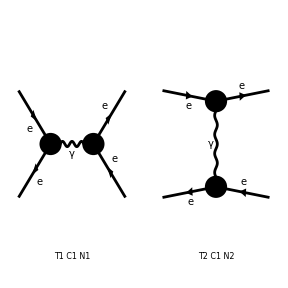

```mathematica
ibb=InsertFields[tbb, {F[2,{1}], -F[2,{1}]} -> {F[2,{1}], -F[2,{1}]}, QEDOnly, InsertionLevel->Classes];
Paint[ibb,PaintLevel->{Classes}];
```

## One-Loop

```mathematica
tbb1=CreateTopologies[1,2->2, Adjacencies->3,ExcludeTopologies->{Tadpoles,WFCorrections,Triangles}];
Paint[tbb1];
```

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 4 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 5 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 6 aebf/cfde/egfhghgh.m, 0 diagrams

-Graphics-

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Classes}

> Top. 1: 2 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 3 Classes insertions

> Top. 5: 3 Classes insertions

> Top. 6: 0 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 10 Classes insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 4 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 5 aebf/cedf/egfhghgh.m, 0 diagrams

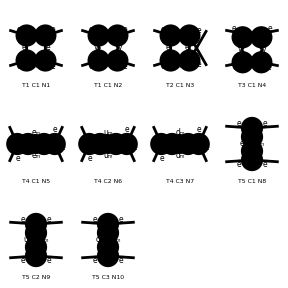

```mathematica
ibb1=InsertFields[tbb1, {F[2,{1}], -F[2,{1}]} -> {F[2,{1}], -F[2,{1}]}, QEDOnly, InsertionLevel->{Classes}];
Paint[ibb1,PaintLevel->{Classes}, ColumnsXRows->4];
```

## Møller Scattering - e^- e^- -> e^- e^-

## Tree-Level

```mathematica
tmo=CreateTopologies[0,2->2, Adjacencies->3];
Paint[tmo];
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

-Graphics-

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 1 Generic, 1 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 2 Generic, 2 Classes insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

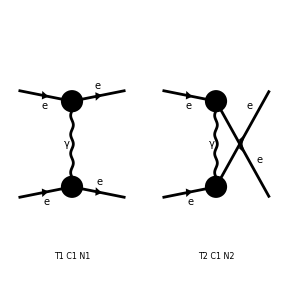

```mathematica
imo=InsertFields[tmo, {F[2,{1}], F[2,{1}]} -> {F[2,{1}], F[2,{1}]}, QEDOnly, InsertionLevel->Classes];
Paint[imo,PaintLevel->{Classes}];
```

## One-Loop

```mathematica
tmo1=CreateTopologies[1,2->2, Adjacencies->3,ExcludeTopologies->{Tadpoles,WFCorrections,Triangles}];
Paint[tmo1];
```

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 4 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 5 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 6 aebf/cfde/egfhghgh.m, 0 diagrams

-Graphics-

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 2 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 3 Classes insertions

> Top. 6: 3 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 10 Classes insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 4 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 5 aebf/cfde/egfhghgh.m, 0 diagrams

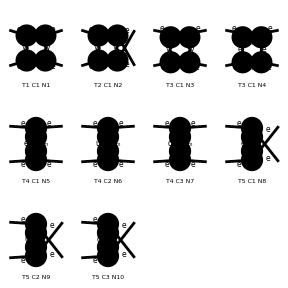

```mathematica
imo1=InsertFields[tmo1, {F[2,{1}], F[2,{1}]} -> {F[2,{1}], F[2,{1}]}, QEDOnly, InsertionLevel->{Classes}];
Paint[imo1,PaintLevel->{Classes}, ColumnsXRows->4];
```

## Electron-Positron Annihilation - e^- e^- -> e^- e^-

## Tree-Level

```mathematica
tep=CreateTopologies[0,2->2, Adjacencies->3];
Paint[tep];
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

-Graphics-

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 1 Generic, 1 Classes insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 2 Generic, 2 Classes insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

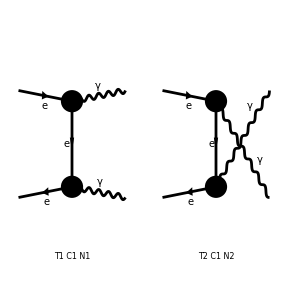

```mathematica
iep=InsertFields[tep, {F[2,{1}], -F[2,{1}]} -> {V[1], V[1]}, QEDOnly, InsertionLevel->Classes];
Paint[iep,PaintLevel->{Classes}];
```

## One-Loop

```mathematica
tep1=CreateTopologies[1,2->2, Adjacencies->3,ExcludeTopologies->{Tadpoles,WFCorrections,Triangles}];
Paint[tep1];
```

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 4 aebe/cfdf/egfhghgh.m, 0 diagrams

> Top. 5 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 6 aebf/cfde/egfhghgh.m, 0 diagrams

-Graphics-

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 1 Classes insertion

> Top. 6: 1 Classes insertion

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 4 Classes insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cedf/egfhghgh.m, 0 diagrams

> Top. 4 aebf/cfde/egfhghgh.m, 0 diagrams

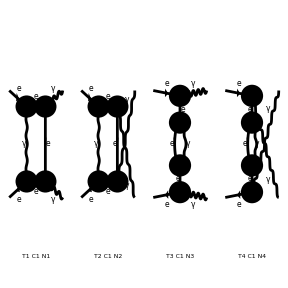

```mathematica
imo1=InsertFields[tmo1, {F[2,{1}], -F[2,{1}]} -> {V[1], V[1]}, QEDOnly, InsertionLevel->{Classes}];
Paint[imo1,PaintLevel->{Classes}, ColumnsXRows->4];
```